## Question 3)b)

### Define the cubic equation for rc

```mathematica
cubic[r_, M_, a_] = r (r-3 M)^2-4 a^2 M
```

-4 a^2 M+r (-3 M+r)^2

### Define the Light Ring prograde/retrograde equations for r .

```mathematica
rLRprograde[M_,a_] = 2 M (1+Cos[2/3*ArcCos[a/M]])
```

2 M (1+Cos[2/3 ArcCos[a/M]])

```mathematica
rLRretrograde[M_,a_] = 2 M (1+Cos[2/3*ArcCos[-a/M]])
```

2 M (1+Cos[2/3 ArcCos[-a/M]])

### Put the Light ring equations into the cubic equation and see if it evaluates to zero . If it does, then (5.18) is numerically verified .

```mathematica
cubic[rLRprograde[M,a],M,a]//Simplify
```

0

```mathematica
cubic[rLRretrograde[M,a],M,a]//Simplify
```

0

### Second method: Plot r(r-3M)^2 and 4a^2M vs a ∈[0,1] as suggested in the question

1

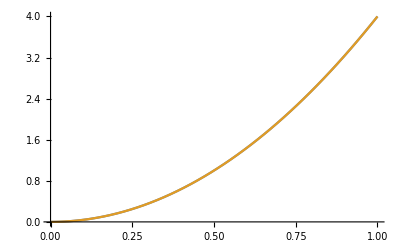

```mathematica
M = 1
Plot[{rLRprograde[M,a](rLRprograde[M,a]-3 M)^2, 4 a^2 M},{a,0,1}]
```

```mathematica
Plot[{rLRretrograde[M,a](rLRretrograde[M,a]-3 M)^2, 4 a^2 M},{a,0,1}]
```

-Graphics-

### In each plot, two curves are graphed exactly on top of each other, showing that Eq. 5.18 is a solution to Eq 5.17.

## Question 4)a)

```mathematica
Clear[M]
```

### Define terms

```mathematica
Δ = r^2 - 2 M r + a^2
```

a^2-2 M r+r^2

### equation (5.7a)

```mathematica
tdot[r_,e_,L_] = ((r^2 + a^2 + 2 M a^2/r) e - 2 M a L / r)/Δ
```

(-(2 a L M)/r+e (a^2+(2 a^2 M)/r+r^2))/(a^2-2 M r+r^2)

### equation (5.7 b)

```mathematica
phidot[r_,e_,L_] = ((1-2 M /r) L + 2 M a e / r)/Δ
```

L (1-(2 M)/r)+(2 a e M)/r

### Q+ and Q-

```mathematica
qplus = 1-3 M u + 2 a Sqrt[M u^3]
```

1-3 M u+2 a √(M u^3)

```mathematica
qminus = 1-3 M u - 2 a Sqrt[M u^3]
```

1-3 M u-2 a √(M u^3)

### Equation (5.31)

```mathematica
eprograde=1/Sqrt[qplus] (1 - 2 M u + a Sqrt[M u^3])
```

(1-2 M u+a √(M u^3))/(√(1-3 M u+2 a √(M u^3)))

```mathematica
eretrograde=1/Sqrt[qminus] (1 - 2 M u - a Sqrt[M u^3])
```

(1-2 M u-a √(M u^3))/(√(1-3 M u-2 a √(M u^3)))

### Equation (5.32)

```mathematica
Lprograde = Sqrt[M/(u qplus)] (a^2 u^2 + 1 - 2 a Sqrt[M u^3])
```

(1+a^2 u^2-2 a √(M u^3)) √(M/(u (1-3 M u+2 a √(M u^3))))

```mathematica
Lretrograde = -Sqrt[M/(u qminus)] (a^2 u^2 + 1 + 2 a Sqrt[M u^3])
```

-√(M/(u (1-3 M u-2 a √(M u^3)))) (1+a^2 u^2+2 a √(M u^3))

### Attempt to evaluate Ω = phidot/tdot

```mathematica
Ωprograde = FullSimplify[phidot[1/u,eprograde,Lprograde]/tdot[1/u,eprograde,Lprograde]]
```

((2 a M u (1-2 M u+a √(M u^3)))/(√(1-3 M u+2 a √(M u^3)))+(1-2 M u) (1+a^2 u^2-2 a √(M u^3)) √(M/(u-3 M u^2+2 a u √(M u^3))))/(-2 a M u (1+a^2 u^2-2 a √(M u^3)) √(M/(u-3 M u^2+2 a u √(M u^3)))+((1-2 M u+a √(M u^3)) (1/u^2+a^2 (1+2 M u)))/(√(1-3 M u+2 a √(M u^3))))

```mathematica
Ωretrograde = Simplify[phidot[1/u,eretrograde,Lretrograde]/tdot[1/u,eretrograde,Lretrograde]]
```

(-(2 a M u (-1+2 M u+a √(M u^3)))/(√(1-3 M u-2 a √(M u^3)))+(-1+2 M u) (1+a^2 u^2+2 a √(M u^3)) √(M/(u-3 M u^2-2 a u √(M u^3))))/(2 a M u (1+a^2 u^2+2 a √(M u^3)) √(M/(u-3 M u^2-2 a u √(M u^3)))+((1-2 M u-a √(M u^3)) (1/u^2+a^2 (1+2 M u)))/(√(1-3 M u-2 a √(M u^3))))

### Unsuccessful. Does Ωprograde==(5.33)?

```mathematica
Ωprograde ==Sqrt[M]/(1/u^(3/2)+a Sqrt[M])//Simplify
```

((2 a M u (1-2 M u+a √(M u^3)))/(√(1-3 M u+2 a √(M u^3)))+(1-2 M u) (1+a^2 u^2-2 a √(M u^3)) √(M/(u-3 M u^2+2 a u √(M u^3))))/(-2 a M u (1+a^2 u^2-2 a √(M u^3)) √(M/(u-3 M u^2+2 a u √(M u^3)))+((1-2 M u+a √(M u^3)) (1/u^2+a^2 (1+2 M u)))/(√(1-3 M u+2 a √(M u^3))))==(√M)/(a √M+1/u^(3/2))

### Apparently Ωprograde != (5.33). Do the second approach by evaluating the roots of the quadratic for Ω.

```mathematica
Simplify[(4 M a u + Sqrt[16 M^2 a^2 u^2 - 4 (1/tdot[1/u,e,L]-(1-2 M u)) (1/u^2 + a^2 + 2 M a^2 u)])/(2(1/u^2 + a^2 + 2 M a^2 u))]
```

(4 a M u+√(16 a^2 M^2 u^2-4 (1/u^2+a^2 (1+2 M u)) (-1+2 M u+(1-2 M u+a^2 u^2)/(e-2 a L M u^3+a^2 e u^2 (1+2 M u)))))/(2 (1/u^2+a^2 (1+2 M u)))

### Did not simplify